```mathematica
(* general donut properties *)
```

```mathematica
utt[ell_,r_,a_,θ_]:=-1/(√(-(8 a ell r)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 θ]))+(a^4+2 r^4+a^2 r (2+3 r)+a^2 (a^2+(-2+r) r) Cos[2 θ])/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 θ]))-(2 ell^2 ((-2+r) r+a^2 Cos[θ]^2) Csc[θ]^2)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 θ]))));
```

```mathematica
HatR[ell_,UTPOT_,GAMMA_,KKK_,a_,R_]:=
(
thsol=NSolve[utt[ell,R,a,θ]/UTPOT==-1,θ]//Quiet;
{Cos[thsol[[2,1,2]]]R}
);
```

```mathematica
HatR[4.5,0.9715,4/3,10^3,0,16]
```

{3.60193}

```mathematica
UTPOTatRH[ell_,GAMMA_,KKK_,a_,R_,H_]:=
(
solut=NSolve[HatR[ell,utpot,GAMMA,KKK,a,R]==H,utpot];
{solut[[2,1,2]]}
);
```

```mathematica
UTPOTatRH[4.5,4/3,10^3,0,16,3.5]
```

{0.971387}

```mathematica
(* rad hydro donut *)
```

```mathematica
donutrhd[M_,ell_,UTPOT_,GAMMA_,KKK_,a_,r_,θ_]:=
(
(* scaling *)
MASSCM=M 147700;
GGG=6.674 10^-8;
CCC=2.998 10^10;
KBOLTZ=1.38 10^-16 GGG/CCC^4/MASSCM;
MPROTON=1.67 10^-24 GGG/CCC^2/MASSCM;
SIGMARAD=5.67 10^-5 GGG/CCC^5 MASSCM^2;
MUGAS=1;
(* Kerr metric *)
ρ2=r^2+a^2 Cos[θ]^2;
Δ=r^2-2r+a^2;
g00=-(1-(2r)/ρ2);
g03=g30=-(2r)/ρ2 a Sin[θ]^2;
g11=ρ2/Δ;
g22=ρ2;
g33=(r^2+a^2+(2r)/ρ2 a^2 Sin[θ]^2)Sin[θ]^2;
g01=g02=g10=g12=g13=g20=g21=g23=g31=g32=0;
(* matrix form *)
g={{g00,g01,g02,g03},{g10,g11,g12,g13},{g20,g21,g22,g23},{g30,g31,g32,g33}};
G=Simplify[Inverse[g]];
G00=G[[1,1]];G01=G[[1,2]];G02=G[[1,3]];G03=G[[1,4]];
G10=G[[2,1]];G11=G[[2,2]];G12=G[[2,3]];G13=G[[2,4]];
G20=G[[3,1]];G21=G[[3,2]];G22=G[[3,3]];G23=G[[3,4]];
G30=G[[4,1]];G31=G[[4,2]];G32=G[[4,3]];
G33=G[[4,4]];

(* donut solution *)
podpierd=-(G00-2 ell G03+ell ell G33);
ut=-1/√podpierd;
ut=ut/UTPOT;
If[podpierd≥0 && ut>-1,
h=-1/ut;
eps=(h-1)/GAMMA;
rho=(eps(GAMMA-1)/KKK)^(1/(GAMMA-1));
uint=rho eps;
P=(GAMMA-1)uint;
aaa=4 SIGMARAD/3;
bbb=KBOLTZ rho/MUGAS/MPROTON;
solT=NSolve[P==aaa T^4+bbb T,T];
T4=solT[[4,1,2]];
uint=KBOLTZ rho T4/MUGAS/MPROTON/(GAMMA-1);
EE=4 SIGMARAD T4^4;
,
rho=0;
uint=0;
EE=0;];
{rho,uint,EE,1/3EE/(uint(GAMMA-1))}
);
```

```mathematica
(* hydro donut *)
```

```mathematica
donuthd[ell_,UTPOT_,GAMMA_,KKK_,a_,r_,θ_]:=
(
(* Kerr metric *)
ρ2=r^2+a^2 Cos[θ]^2;
Δ=r^2-2r+a^2;
g00=-(1-(2r)/ρ2);
g03=g30=-(2r)/ρ2 a Sin[θ]^2;
g11=ρ2/Δ;
g22=ρ2;
g33=(r^2+a^2+(2r)/ρ2 a^2 Sin[θ]^2)Sin[θ]^2;
g01=g02=g10=g12=g13=g20=g21=g23=g31=g32=0;
(* matrix form *)
g={{g00,g01,g02,g03},{g10,g11,g12,g13},{g20,g21,g22,g23},{g30,g31,g32,g33}};
G=Simplify[Inverse[g]];
G00=G[[1,1]];G01=G[[1,2]];G02=G[[1,3]];G03=G[[1,4]];
G10=G[[2,1]];G11=G[[2,2]];G12=G[[2,3]];G13=G[[2,4]];
G20=G[[3,1]];G21=G[[3,2]];G22=G[[3,3]];G23=G[[3,4]];
G30=G[[4,1]];G31=G[[4,2]];G32=G[[4,3]];
G33=G[[4,4]];

(* donut solution *)
podpierd=-(G00-2 ell G03+ell ell G33);
ut=-1/√podpierd;
ut=ut/UTPOT;
If[podpierd≥0 && ut>-1,
h=-1/ut;
eps=(h-1)/GAMMA;
rho=(eps(GAMMA-1)/KKK)^(1/(GAMMA-1));
uint=rho eps;
,
rho=0;
uint=0;];
{rho,uint}
);
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

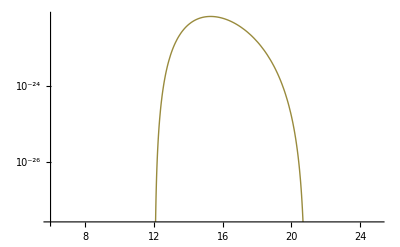

```mathematica
LogPlot[{donuthd[4.5,0.9715,4/3,10^3,0,rr,π/2][[2]](GAMMA-1),donutrhd[10,4.5,0.9715,4/3,10^3,0,rr,π/2][[2]](GAMMA-1),1/3donutrhd[10,4.5,0.9715,4/3,10^3,0,rr,π/2][[3]]},{rr,6,25}]
```

```mathematica
(*DensityPlot[Log[donuthd[4.5,0.9715,4/3,10^3,0,√(xx^2+yy^2),ArcTan[xx/yy]][[1]]],{xx,10,20},{yy,0,10}]*)
```

```mathematica
(* manual integration *)
mysigma[M_,ell_,UTPOT_,GAMMA_,KKK_,a_,r_,thmin_]:=
(
dth=(π/2-thmin)/100;
sigma=0;
For[i=0,i<100,i++,
th1=thmin+i dth;
th2=th1+dth;
sigma=sigma+1/2(donuthd[ell,UTPOT,GAMMA,KKK,a,r,th1][[1]] CCC^2/(GGG MASSCM^2)r Sin[th1] MASSCM +donuthd[ell,UTPOT,GAMMA,KKK,a,r,th2][[1]] CCC^2/(GGG MASSCM^2)r Sin[th2] MASSCM)
];
sigma
);
mysigmatot[M_,ell_,UTPOT_,GAMMA_,KKK_,a_,r_]:=
(
dth=(π/2-0.1)/100;
sigma=0;
For[i=0,i<100,i++,
th1=0.1+i dth;
th2=th1+dth;
sigma=sigma+1/2(donuthd[ell,UTPOT,GAMMA,KKK,a,r,th1][[1]] CCC^2/(GGG MASSCM^2)r Sin[th1] MASSCM +donuthd[ell,UTPOT,GAMMA,KKK,a,r,th2][[1]] CCC^2/(GGG MASSCM^2)r Sin[th2] MASSCM)dth
];
sigma
);
```

```mathematica
(* surface density calculator *)
```

```mathematica
sigmacgs[M_,ell_,UTPOT_,GAMMA_,KKK_,a_,r_]:=
(
(* scaling *)
MASSCM=M 147700;
GGG=6.674 10^-8;
CCC=2.998 10^10;
thmin=π/2-ArcSin[HatR[ell,UTPOT,GAMMA,KKK,a,r]/r][[1]];
(*sigma=2NIntegrate[(donuthd[ell,UTPOT,GAMMA,KKK,a,r,th][[1]]) CCC^2/(GGG MASSCM^2)r Sin[th] MASSCM ,{th,1.001thmin,π/2},Method->"AdaptiveMonteCarlo"];*)
sigma=mysigma[M,ell,UTPOT,GAMMA,KKK,a,r,thmin];
{sigma,thmin}
)
```

```mathematica
(* solves for KKK for given sigma *)
```

```mathematica
KKKfromsigma[M_,ell_,UTPOT_,GAMMA_,a_,r_,Σ_]:=
(
sol=FindRoot[Σ==mysigmatot[M,ell,UTPOT,GAMMA,KKK,a,r],{KKK,10^1}];
{sol}
)
```

```mathematica
mysigmatot[10.,4.5,.988,4/3,10^5,0,16]
```

4.69932

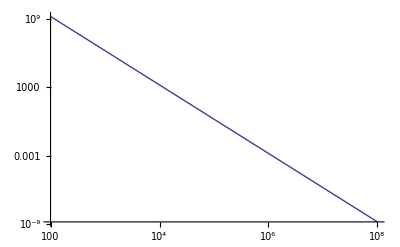

```mathematica
LogLogPlot[mysigmatot[10.,4.5,.983,4/3,KKK,0,16],{KKK,100,10^8},PlotPoints->10]
```

```mathematica
donuthd[4.5,0.9715,4/3,10^3,0,16,1.5]
```

{9.16463×10^-20,1.23958×10^-22}

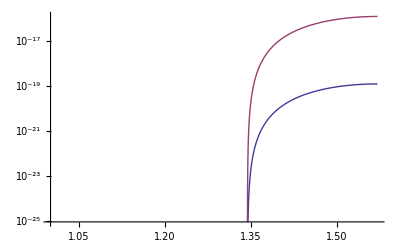

```mathematica
LogPlot[{donuthd[4.5,0.9715,4/3,10^3,0,16,th][[1]],donuthd[4.5,0.9715,4/3,10^2,0,16,th][[1]]},{th,1,π/2}]
```

```mathematica
MASSCM=10 147700;
GGG=6.674 10^-8;
CCC=2.998 10^10;
NIntegrate[Evaluate[donuthd[4.5,0.9715,4/3,10^3,0,16,th][[1]] CCC^2/(GGG MASSCM^2)16 Sin[th] MASSCM ],{th,1.4,1.5},Method->MonteCarlo]
```

1.2329×10^-8

```mathematica
donuthd[4.5,0.9715,4/3,10^3,0,16,π/2][[1]] CCC^2/(GGG MASSCM^2)16 MASSCM
```

17985.2